```mathematica
(*with rfd, 5000 non interacting particles*)
SetDirectory[NotebookDirectory[]];
dir="/home/drladiges/gigan/projects/FHDeX/exec/";
(*dir="/home/drladiges/gigan/projects/FHDeX/exec/";*)
file="asciiVx000025000";
count=2;
slist={"E","F"};
(*slist={"E","F","G","H"};*)(*eo damp 0*)
(*slist={"I","J","K","L"};*)(*eo wet 120*)
(*slist={""};*)
rawList=Table[0,{ii,1,count}];
(*dir="/home/drladiges/projects/FHDeX/exec/";.
file="ascii_means000000150";*)

For[kk=1,kk≤count,kk++,
raw0=Import[dir<>"immersedIons"<>slist[[kk]]<>"/0_"<>file,"Table"];
raw1=Import[dir<>"immersedIons"<>slist[[kk]]<>"/1_"<>file,"Table"];
raw2=Import[dir<>"immersedIons"<>slist[[kk]]<>"/2_"<>file,"Table"];
raw3=Import[dir<>"immersedIons"<>slist[[kk]]<>"/3_"<>file,"Table"];
raw4=Import[dir<>"immersedIons"<>slist[[kk]]<>"/4_"<>file,"Table"];
raw5=Import[dir<>"immersedIons"<>slist[[kk]]<>"/5_"<>file,"Table"];
raw6=Import[dir<>"immersedIons"<>slist[[kk]]<>"/6_"<>file,"Table"];
raw7=Import[dir<>"immersedIons"<>slist[[kk]]<>"/7_"<>file,"Table"];
(*rawA=Join[raw0[[1;;-3]],raw1[[1;;-3]],raw2[[1;;-3]],raw3[[1;;-3]]];*)
rawA=Join[raw0[[1;;-3]],raw1[[1;;-3]],raw2[[1;;-3]],raw3[[1;;-3]],raw4[[1;;-3]],raw5[[1;;-3]],raw6[[1;;-3]],raw7[[1;;-3]]];
rawList[[kk]]=rawA/.{}->Nothing;
];
```

```mathematica
xsize=128;
ysize=128;
zsize=64;a
(*xsize=64;
ysize=64;
zsize=32;*)
cell=1;

func3D=Table[0,{ii,1,count}];
func2D=Table[0,{ii,1,count}];

For[ll=1,ll≤count,ll++,
members3DA=Table[{ToExpression[StringReplace[rawList[[ll,ii,1]],{"("-> "{",")"-> "}"}]],rawList[[ll,ii,2]]},{ii,1,Length[rawList[[ll]]]}];
members3DA= DeleteDuplicatesBy[members3DA,First];
func3D[[ll]]=Interpolation[members3DA,InterpolationOrder->0];
membersFlat=Flatten[Table[{{ii,jj},Mean[Table[func3D[[ll]][ii,jj,kk],{kk,0,zsize-1,cell}]]},{ii,0,xsize-1},{jj,0,ysize-1}],1];
func2D[[ll]]=Interpolation[membersFlat,InterpolationOrder->0];
];
```

a

```mathematica
func2DM[x_,y_] = Sum[func2D[[ll]][x,y],{ll,1,count}]/count;
```

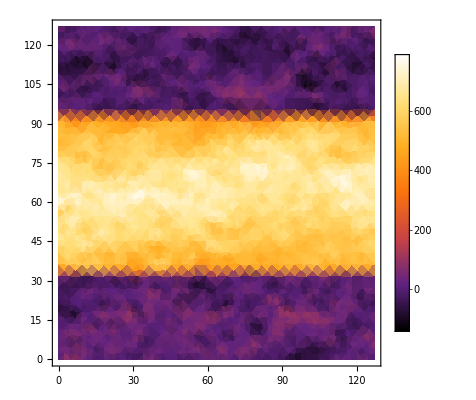

```mathematica
DensityPlot[func2DM[x,y],{x,0,xsize-1},{y,0,ysize-1},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

```mathematica
membersFlatter=Flatten[Table[{{jj,Mean[Table[func2DM[ii,jj],{ii,0,xsize-1,cell}]]}},{jj,0,ysize-1}],1];
func1DM=Interpolation[membersFlatter,InterpolationOrder->1];
```

```mathematica
(*size=8.284925963482451*10^-7;*)
size=13.06*10^-7;
dx=size/xsize;
posFunc[x_]=x/dx -0.5;


m1=Graphics[{Thick,Red,Circle[{0,0},1]}];
m2=Graphics[{Thick,Black,Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}];
m3=Graphics[{Thick,Purple,Line[{{-0.5,-0.5},{0.5,0.5}}],Line[{{-0.5,0.5},{0.5,-0.5}}]}];
m4=Graphics[{Thick,Green,Line[{{0,-0.5},{-0.5,0},{0,0.5},{0.5,0},{0,-0.5}}]}];

ml1=Graphics[Line[{{0.25size,-20},{0.25size,900}}]];
ml2=Graphics[Line[{{0.75size,-20},{0.75size,900}}]];
```

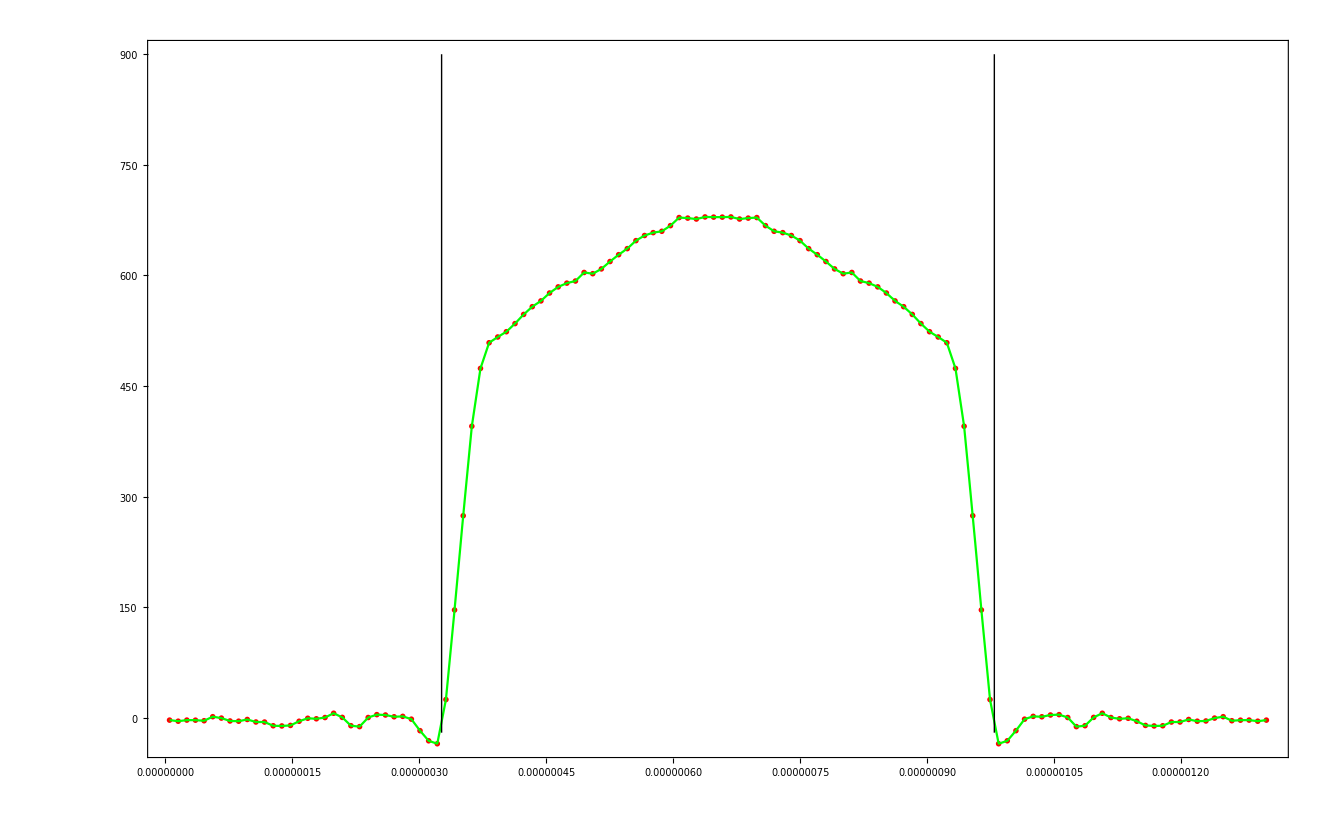

```mathematica
pa=ListPlot[Table[{y,(func1DM[posFunc[size-y]]+func1DM[posFunc[y]])/2},{y,dx/2,size-dx/2,dx}],PlotStyle->Red,PlotMarkers->{m4,0.03}];
pb=Plot[(func1DM[posFunc[size-y]]+func1DM[posFunc[y]])/2,{y,dx/2,size-dx/2},PlotRange->All,PlotStyle->Green];
Show[pa,pb,ml1,ml2,PlotRange->All,Frame->True,Axes->True]
```

```mathematica
func1DM[posFunc[size/2]]
```

875.266

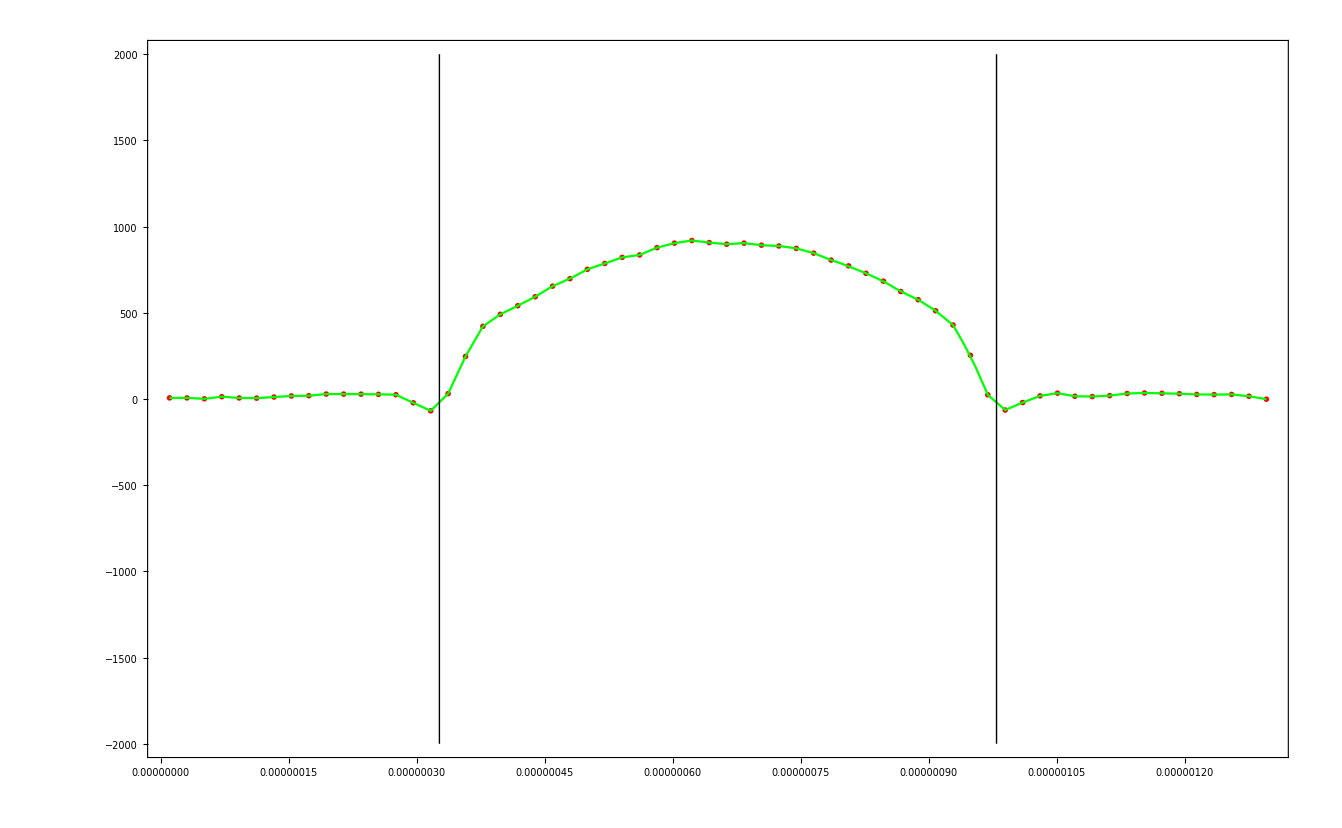

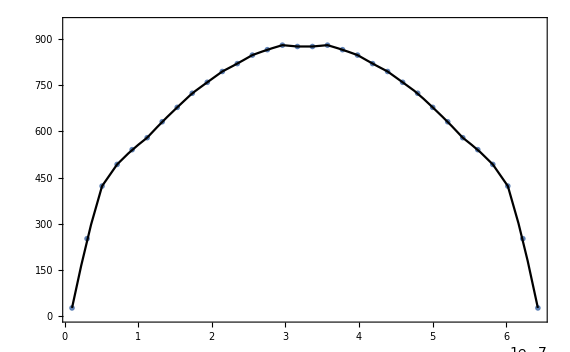

```mathematica
pa=ListPlot[Table[{y,(func1DM[posFunc[size-(y+0.25size)]]+func1DM[posFunc[(y+0.25size)]])/2},{y,dx/2,0.5size-dx/2,dx}],PlotMarkers->{m2,0.03},PlotRange->{0,900}];
pb=Plot[(func1DM[posFunc[size-(y+0.25size)]]+func1DM[posFunc[y+0.25size]])/2,{y,dx/2,0.5size-dx/2},PlotStyle->Black,PlotRange->{0,900}];
Show[pa,pb,Frame->True,Axes->False,AxesOrigin->{0,0},PlotRange->{0,950}]
```

```mathematica
raw0
```

{{(-1,-1,-1),-1807.57},{(0,-1,-1),-509.774},{(1,-1,-1),-761.79},{(2,-1,-1),-53.5766},{(3,-1,-1),-3248.13},{(4,-1,-1),-1782.77},{(5,-1,-1),615.691},{(6,-1,-1),-117.47},{(7,-1,-1),-732.151},{(8,-1,-1),-2205.6},{(9,-1,-1),-1214.45},{(10,-1,-1),-1176.94},{(11,-1,-1),194.981},{(12,-1,-1),1412.16},{(13,-1,-1),37.7184},{(14,-1,-1),569.837},{(15,-1,-1),-2839.23},42810,{(19,32,32),783093},{(20,32,32),779846},{(21,32,32),775139},{(22,32,32),768474},{(23,32,32),764399},{(24,32,32),762698},{(25,32,32),759819},{(26,32,32),750378},{(27,32,32),758964},{(28,32,32),755170},{(29,32,32),752716},{(30,32,32),752095},{(31,32,32),752436},{(32,32,32),752509},{(33,32,32),753058},{},{}}
 |  |  |  |

```mathematica
Table[{ToExpression[StringReplace[rawList[[1,ii,1]],{"("-> "{",")"-> "}"}]],rawList[[1,ii,2]]},{ii,1,Length[rawList[[ll]]]/2}]
```

Part::partw: Part 1 of {} does not exist.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{{(-1,-1,-1),-1159.08},{(0,-1,-1),-2754.51},{(1,-1,-1),-2071.41},{(2,-1,-1),413.786},{(3,-1,-1),2414.11},{(4,-1,-1),-315.704},{(5,-1,-1),-2716.53},{(6,-1,-1),698.289},{(7,-1,-1),-249.651},{(8,-1,-1),-508.548},{(9,-1,-1),-792.863},{(10,-1,-1),-2685},{(11,-1,-1),-52.2295},{(12,-1,-1),2393.43},{(13,-1,-1),1458.91},{(14,-1,-1),-1190.72},«19»,{(-1,0,-1),1159.08},{(0,0,-1),2754.51},{(1,0,-1),2071.41},{(2,0,-1),-413.786},{(3,0,-1),-2414.11},{(4,0,-1),315.704},{(5,0,-1),2716.53},{(6,0,-1),-698.289},{(7,0,-1),249.651},{(8,0,-1),508.548},{(9,0,-1),792.863},{(10,0,-1),2685},{(11,0,-1),52.2295},{(12,0,-1),-2393.43},{(13,0,-1),-1458.91},«171318»},{«1»},{«1»},{«1»}}⟦«1»⟧,«1»].

ToExpression::notstrbox: StringReplace[{{{(-1,-1,-1),-1159.08},{(0,-1,-1),-2754.51},{(1,-1,-1),-2071.41},{(2,-1,-1),413.786},{(3,-1,-1),2414.11},{(4,-1,-1),-315.704},{(5,-1,-1),-2716.53},{(6,-1,-1),698.289},{(7,-1,-1),-249.651},{(8,-1,-1),-508.548},{(9,-1,-1),-792.863},{(10,-1,-1),-2685},{(11,-1,-1),-52.2295},{(12,-1,-1),2393.43},{(13,-1,-1),1458.91},{(14,-1,-1),-1190.72},«19»,{(-1,0,-1),1159.08},{(0,0,-1),2754.51},{(1,0,-1),2071.41},{(2,0,-1),-413.786},{(3,0,-1),-2414.11},{(4,0,-1),315.704},{(5,0,-1),2716.53},{(6,0,-1),-698.289},{(7,0,-1),249.651},{(8,0,-1),508.548},{(9,0,-1),792.863},{(10,0,-1),2685},{(11,0,-1),52.2295},{(12,0,-1),-2393.43},{(13,0,-1),-1458.91},«171318»},{«1»},{«1»},{«1»}}⟦«1»⟧,«1»] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{{(-1,-1,-1),-1159.08},{(0,-1,-1),-2754.51},{(1,-1,-1),-2071.41},{(2,-1,-1),413.786},{(3,-1,-1),2414.11},{(4,-1,-1),-315.704},{(5,-1,-1),-2716.53},{(6,-1,-1),698.289},{(7,-1,-1),-249.651},{(8,-1,-1),-508.548},{(9,-1,-1),-792.863},{(10,-1,-1),-2685},{(11,-1,-1),-52.2295},{(12,-1,-1),2393.43},{(13,-1,-1),1458.91},{(14,-1,-1),-1190.72},«19»,{(-1,0,-1),1159.08},{(0,0,-1),2754.51},{(1,0,-1),2071.41},{(2,0,-1),-413.786},{(3,0,-1),-2414.11},{(4,0,-1),315.704},{(5,0,-1),2716.53},{(6,0,-1),-698.289},{(7,0,-1),249.651},{(8,0,-1),508.548},{(9,0,-1),792.863},{(10,0,-1),2685},{(11,0,-1),52.2295},{(12,0,-1),-2393.43},{(13,0,-1),-1458.91},«171318»},{«1»},{«1»},{«1»}}⟦«1»⟧,«1»].

ToExpression::notstrbox: StringReplace[{{{(-1,-1,-1),-1159.08},{(0,-1,-1),-2754.51},{(1,-1,-1),-2071.41},{(2,-1,-1),413.786},{(3,-1,-1),2414.11},{(4,-1,-1),-315.704},{(5,-1,-1),-2716.53},{(6,-1,-1),698.289},{(7,-1,-1),-249.651},{(8,-1,-1),-508.548},{(9,-1,-1),-792.863},{(10,-1,-1),-2685},{(11,-1,-1),-52.2295},{(12,-1,-1),2393.43},{(13,-1,-1),1458.91},{(14,-1,-1),-1190.72},«19»,{(-1,0,-1),1159.08},{(0,0,-1),2754.51},{(1,0,-1),2071.41},{(2,0,-1),-413.786},{(3,0,-1),-2414.11},{(4,0,-1),315.704},{(5,0,-1),2716.53},{(6,0,-1),-698.289},{(7,0,-1),249.651},{(8,0,-1),508.548},{(9,0,-1),792.863},{(10,0,-1),2685},{(11,0,-1),52.2295},{(12,0,-1),-2393.43},{(13,0,-1),-1458.91},«171318»},{«1»},{«1»},{«1»}}⟦«1»⟧,«1»] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

$Aborted

```mathematica
rawList[[1,-1,1]]
```

(65,64,32)

```mathematica
L
```

```mathematica
Position[rawList[[1]],{}]
```

{{21421},{21422},{64263},{64264},{107105},{107106},{149947},{149948}}

```mathematica
rawList[[1,21420]]
rawList[[1,21421]]
```

{(33,32,16),667179}

{}

```mathematica
rawList[[1]]/.{}->Nothing
```

{{(-1,-1,-1),-1159.08},{(0,-1,-1),-2754.51},{(1,-1,-1),-2071.41},{(2,-1,-1),413.786},{(3,-1,-1),2414.11},{(4,-1,-1),-315.704},{(5,-1,-1),-2716.53},{(6,-1,-1),698.289},{(7,-1,-1),-249.651},{(8,-1,-1),-508.548},{(9,-1,-1),-792.863},{(10,-1,-1),-2685},{(11,-1,-1),-52.2295},{(12,-1,-1),2393.43},{(13,-1,-1),1458.91},{(14,-1,-1),-1190.72},171329,{(51,64,32),-1685.03},{(52,64,32),-990.3},{(53,64,32),327.265},{(54,64,32),-2098.2},{(55,64,32),-1860.8},{(56,64,32),791.891},{(57,64,32),-123.527},{(58,64,32),-1343.3},{(59,64,32),680.348},{(60,64,32),1491.31},{(61,64,32),1329.3},{(62,64,32),-897.288},{(63,64,32),-1229.49},{(64,64,32),-4327.59},{(65,64,32),343.885}}
 |  |  |  |